{{y→InterpolatingFunction[{{0., 30.}}, <>]}}

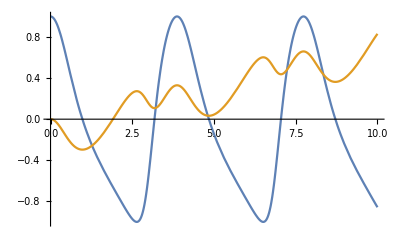

```mathematica
s=NDSolve[{y'[t]==(2+Cos[y[t]]Sin[y[t]]-Sin[y[t]]),y[0]==0},y,{t,0,30}]
Plot[Evaluate[{Cos[y[t]],Integrate[-Sin[y[x]]Cos[y[x]],{x,0,t}]}/.s],{t,0,10},PlotRange->All]
```

0.13

3.857

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{y'[t]==0.9999 (0.+0.0307692 h+Cos[«1»] Sin[«1»]),y[0]==0},y,{t,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{y'[t]==0.9999 (0.0307692 h-0.626552 Sin[«1»]+Cos[«1»] Sin[«1»]),y[0]==0},y,{t,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{y'[t]==0.9999 (0.0307692 h-1.2531 Sin[«1»]+Cos[«1»] Sin[«1»]),y[0]==0},y,{t,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

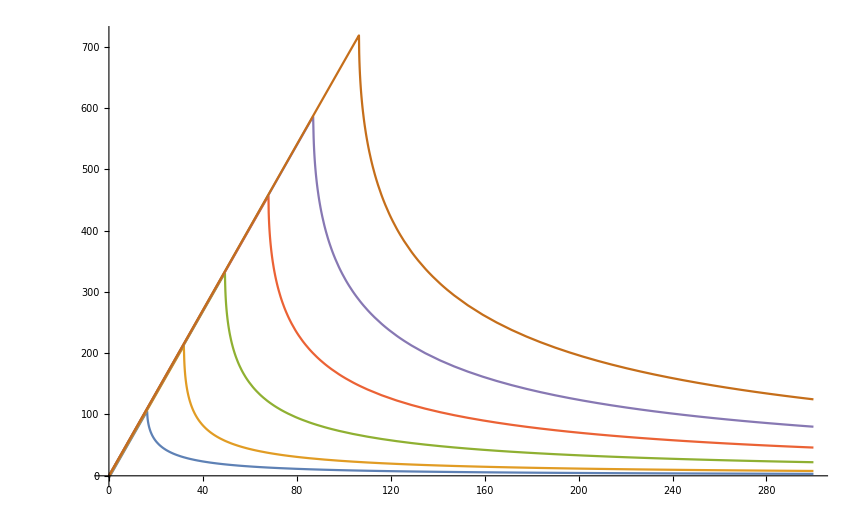

{337.628}

```mathematica
z=0.13
delta=4.055

s[h_,m_]:=NDSolve[{y'[t]==(h*0.004/z+Cos[y[t]]Sin[y[t]]-m*Pi/4/delta/z*Sin[y[t]])/(1+0.01^2),y[0]==0},y,{t,0,100}]
p[h_,m_]:=t/.FindRoot[y[t]==2Pi/.s[h,m],{t,0}]
solve[h_,m_]:=If[y[100]>2Pi,p[h,m],100]
Plot[Evaluate[Table[((h*0.004/z-y[solve[h,m]]/solve[h,m])*439.7*delta*z)/.s[h,m],{m,0,2,0.4}]],{h,0,300},PlotRange->All]
((50*0.004/z-y[solve[50,2]]/solve[50,2])*439.7*delta*z)/.s[50,2]
```

0.1

3.581

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{y'[t]==0.9999 (0.+0.04 h+Cos[«1»] Sin[«1»]),y[0]==0},y,{t,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{y'[t]==0.9999 (0.04 h-0.877295 Sin[«1»]+Cos[«1»] Sin[«1»]),y[0]==0},y,{t,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{y'[t]==0.9999 (0.04 h-1.75459 Sin[«1»]+Cos[«1»] Sin[«1»]),y[0]==0},y,{t,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

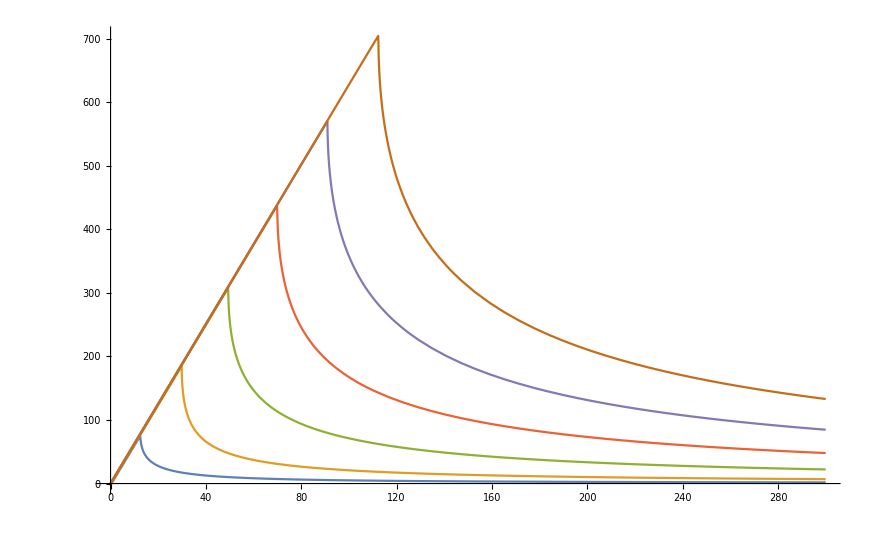

{313.974}

```mathematica
z=0.1
delta=3.581
s[h_,m_]:=NDSolve[{y'[t]==(h*0.004/z+Cos[y[t]]Sin[y[t]]-m*Pi/4/delta/z*Sin[y[t]])/(1+0.01^2),y[0]==0},y,{t,0,100}]
p[h_,m_]:=t/.FindRoot[y[t]==2Pi/.s[h,m],{t,0}]
solve[h_,m_]:=If[y[100]>2Pi,p[h,m],100]
Plot[Evaluate[Table[((h*0.004/z-y[solve[h,m]]/solve[h,m])*439.7*delta*z)/.s[h,m],{m,0,2,0.4}]],{h,0,300},PlotRange->All]
((50*0.004/z-y[solve[50,2]]/solve[50,2])*439.7*delta*z)/.s[50,2]
```